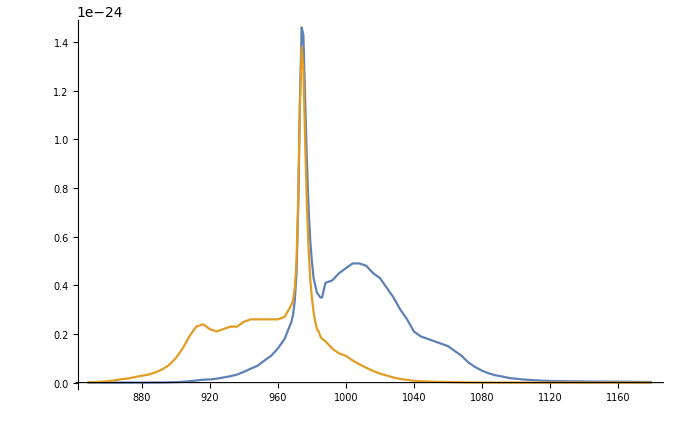

```mathematica
Clear["Global`*"]

(σ=Import[NotebookDirectory[]<>"CrossSection.xls"][[1,5;;,{12,15,16}]])//TableForm;

ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All]

σe=Interpolation[σ[[All,{1,2}]],InterpolationOrder->1];
σa=Interpolation[σ[[All,{1,3}]],InterpolationOrder->1];
```

```mathematica
c=3 10^8;(*м/с*)
τ=100000000;(*1.45 10^-3;*)(*с*)
NN=300;(*ppm*)
NN=6.62 10^22 NN;(*1/м^3*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 7^2 10^-12;(*Эффективная площадь моды*)

λp=960;(*нм*)
λs=1064;(*нм*)
Ps=Aeff h c/(λs 10^-9);
Pp=Aeff h c/(λp 10^-9);

L=2;

σp12=σa[λp];
σp21=σe[λp];
σs12=σa[λs];
σs21=σe[λs];
```

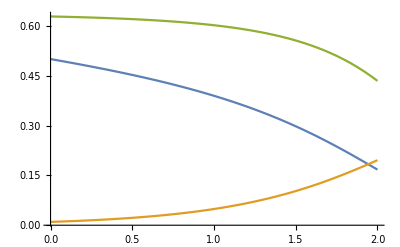

```mathematica
(*Усилитель*)
sol=NDSolve[{ρp[z](σp12 N1[z]-σp21 N2[z])+ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ==0,ρs'[z]==ρs[z](σs21 N2[z]-σs12 N1[z]),
ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z]),
N1[z]+N2[z]==NN,
 Pp ρp[0]==0.5,Ps ρs[0]==10 10^-3},
{ρp,ρs,N1,N2},{z,0,L},AccuracyGoal->-15];

Plot[Evaluate[{Pp ρp[z],Ps ρs[z],N2[z]/NN}/.sol],{z,0,L},PlotRange->All]
```

```mathematica
(*Лазер*)
eqns={ρp[z](σp12 N1[z]-σp21 N2[z])+ρsr[z](σs12 N1[z]-σs21 N2[z])+ρsl[z](σs12 N1[z]-σs21 N2[z])==0,
ρsr'[z]==ρsr[z](σs21 N2[z]-σs12 N1[z]),
ρsl'[z]==-ρsl[z](σs21 N2[z]-σs12 N1[z]),
ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z]),
N1[z]+N2[z]==NN};

solAlEq=Solve[eqns[[{1,5}]],{N1[z],N2[z]}][[1]];
eqns2=Simplify[eqns[[{2,3,4}]]/.solAlEq];
```

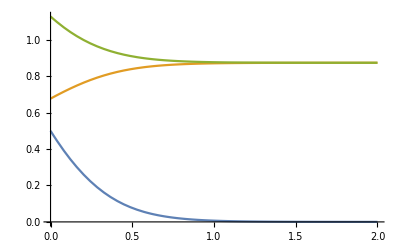

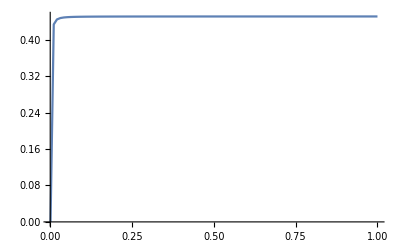

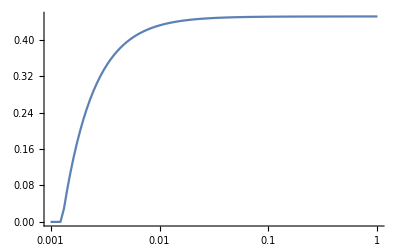

```mathematica
R=0.6;
sol=NDSolve[{eqns2,ρp[0]==0.5/Pp,
ρsr[L]==ρsl[L],ρsr[0]==R ρsl[0]},
{ρp,ρsr,ρsl},{z,0,L},AccuracyGoal->-15,Method->{"Shooting","StartingInitialConditions"->{Ps ρsr[0]==20,Ps ρsl[0]==20}}][[1]];

Plot[Evaluate[{Pp ρp[z],Ps ρsr[z],Ps ρsl[z]}/.sol],{z,0,L},PlotRange->All]

Clear[OutputPower,R]
OutputPower[R_?NumericQ]:=(Ps ρsl[0](1-R))/.(NDSolve[{eqns2,ρp[0]==0.5/Pp,
ρsr[L]==ρsl[L],ρsr[0]==R ρsl[0]},
{ρp,ρsr,ρsl},{z,0,L},AccuracyGoal->-15,Method->{"Shooting","StartingInitialConditions"->{Ps ρsr[0]==20,Ps ρsl[0]==20}}][[1]]);

Plot[OutputPower[R],{R,0.001,1},PlotRange->All,MaxRecursion->1]
LogLinearPlot[OutputPower[R],{R,0.001,1},PlotRange->All,MaxRecursion->1]
```

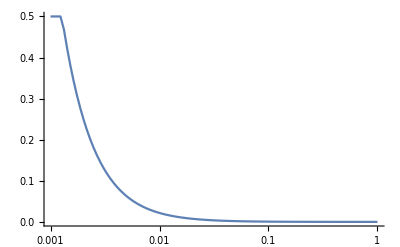

```mathematica
LogLinearPlot[Pp ρp[L]/.(NDSolve[{eqns2,ρp[0]==0.5/Pp,
ρsr[L]==ρsl[L],ρsr[0]==R ρsl[0]},
{ρp,ρsr,ρsl},{z,0,L},AccuracyGoal->-15,Method->{"Shooting","StartingInitialConditions"->{Ps ρsr[0]==20,Ps ρsl[0]==20}}][[1]]),{R,0.001,1},PlotRange->All,MaxRecursion->1]
```

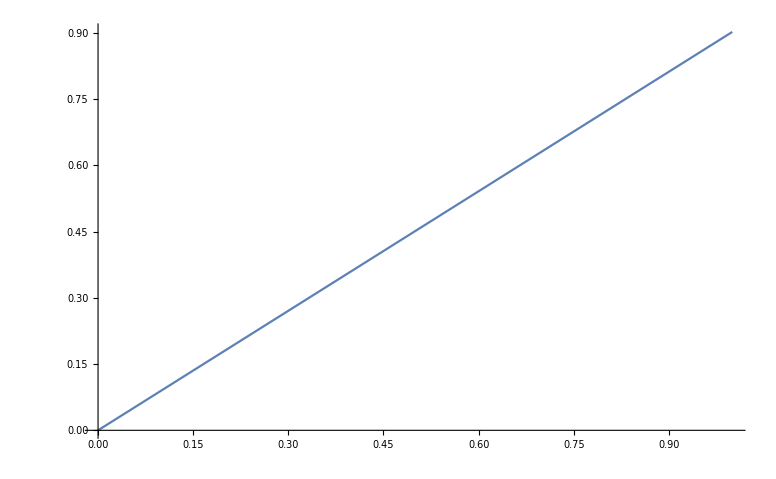

```mathematica
Clear[R];
R=0.6;
OutPow[Pnak_?NumericQ]:=(Ps ρsl[0](1-R))/.(NDSolve[{eqns2,ρp[0]==Pnak/Pp,
ρsr[L]==ρsl[L],ρsr[0]==R ρsl[0]},
{ρp,ρsr,ρsl},{z,0,L},AccuracyGoal->-15,Method->{"Shooting","StartingInitialConditions"->{Ps ρsr[0]==Pnak/2,Ps ρsl[0]==Pnak/2}}][[1]]);
Plot[OutPow[Pnak],{Pnak,0,1},PlotRange->All,MaxRecursion->1]
```

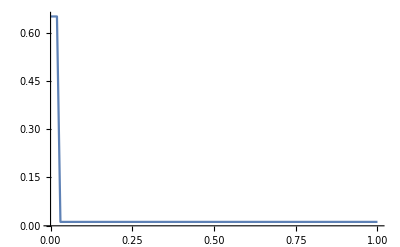

```mathematica
(*Строим долю возбужденных активных ионов от мощности накачки*)
invN2[Pnak_?NumericQ]:=Integrate[(N2[z]/NN/L/.solAlEq/.(NDSolve[{eqns2,ρp[0]==Pnak/Pp,
0.95ρsr[L]==ρsl[L],ρsr[0]==R ρsl[0]},
{ρp,ρsr,ρsl},{z,0,L},AccuracyGoal->-15,Method->{"Shooting","StartingInitialConditions"->{Ps ρsr[0]==Pnak/2,Ps ρsl[0]==Pnak/2}}][[1]])),{z,0,L}];
Plot[invN2[Pnak],{Pnak,0,1},PlotRange->All,MaxRecursion->1]
```

```mathematica
(*Импульсный усилитель*)
n=1.454;
eqnsDyn={ D[N2[z,t],t]==-N2[z,t]/τ+ρp[z,t](σp12 N1[z,t]-σp21 N2[z,t])+ρs[z,t](σs12 N1[z,t]-σs21 N2[z,t]),
D[ρs[z,t],z]+n/c D[ρs[z,t],t]==ρs[z,t](σs21 N2[z,t]-σs12 N1[z,t]),
D[ρp[z,t],z]+n/c D[ρp[z,t],t]==ρp[z,t](σp21 N2[z,t]-σp12 N1[z,t]),
N1[z,t]+N2[z,t]==NN,
ρs[z,0]==100/Ps Exp[-2 (z-L/3)^2/0.1^2] ,
ρp[z,0]==200000/Pp Exp[-2 (z-L/2)^2/0.2^2],
N1[z,0]==NN,N2[z,0]==0};

sol=NDSolve[{eqnsDyn,ρs[L,t]==ρs[0,t],N1[L,t]==N1[0,t],N2[L,t]==N2[0,t]},{ρp,ρs,N1,N2},{z,0,L},{t,0,30 10^-9},AccuracyGoal->-15(*PrecisionGoal->8(*,NormFunction->1*)*),Method->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", MaxPoints->255}}]
```

NDSolve::mxsst: Using maximum number of grid points 255 allowed by the MaxPoints or MinStepSize options for independent variable z.

NDSolve::eerr: Warning: scaled local spatial error estimate of 3.07081×10^8 at t = 3.×10^-8 in the direction of independent variable z is much greater than the prescribed error tolerance. Grid spacing with 255 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{ρp→                                                 -8
InterpolatingFunction[{{…, 0., 2., …}, {0., 3. 10  }}, <>],ρs→                                                 -8
InterpolatingFunction[{{…, 0., 2., …}, {0., 3. 10  }}, <>],N1→                                                 -8
InterpolatingFunction[{{…, 0., 2., …}, {0., 3. 10  }}, <>],N2→                                                 -8
InterpolatingFunction[{{…, 0., 2., …}, {0., 3. 10  }}, <>]}}

```mathematica
Plot3D[Pp ρp[z,t]/.sol,{z,0,L},{t,0,30 10^-9},PlotPoints->40,MaxRecursion->Automatic,
PlotRange->All ]
```

-Graphics3D-

```mathematica
Manipulate[Plot[Pp ρp[z,t]/.sol,{z,0,L},PlotPoints->Automatic,MaxRecursion->Automatic,PlotRange->{0,200000}],{t,0,30 10^-9}]
Manipulate[Plot[Pp ρs[z,t]/.sol,{z,0,L},PlotPoints->Automatic,MaxRecursion->Automatic,PlotRange->All],{t,0,30 10^-9}]
Manipulate[Plot[N2[z,t]/NN/.sol,{z,0,L},PlotPoints->Automatic,MaxRecursion->Automatic,PlotRange->{0,1}],{t,0,30 10^-9}]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Домашнее задание 
1) Быть готовым ответить по физике лазера.
	Перечислить все виды потерь, заложенных в рассматриваемую модель лазера
	Перечислить все известные вам виды потерь, уменьшающие эффективность лазера
	Объяснить возникновение всех характерных точек графика выходной мощности от коэффициента отражения OC решетки. Точки излома, минимума, максимума, причины возрастания и убывания функции на каждом участке графика.
	Уметь объяснить на пальцах, что будет с графиком, если устранять каждый из перечисленных видов потерь.
	Что произойдет с графиком, если увеличивать/уменьшать длину волны сигнала? длину волны накачки?
	Построить ВтВтХ лазера. Объяснить особенности
2) Модель Франца-Нодвика. В среду длиной 3 м с концентрацией ионов 300 ppm, сечением перехода 2.5 пм^2, эффективным диаметром моды 7 мкм падает излучение с длиной волны 1064 нм. Построить график импульса на выходе, энергия в импульсе является параметром задачи. Рассмотреть случай прямоугольного и гауссова импульсов на входе.
	Построить функцию, возвращающую среднеквадратичную длительность импульса и его среднюю координату (первый и второй момент)
3) Посмотреть на реализованное моделирование импульсного усиления в кольцевом лазере. Уметь объяснить, что происходит с накачкой, сигналом и инверсией во времени.